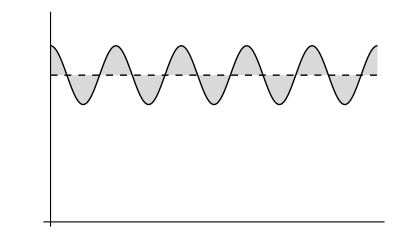

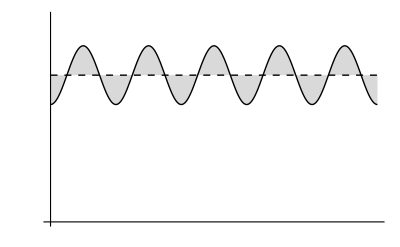

```mathematica
Plot[{1,1+0.1 Cos[π x]},{x,0,10},PlotStyle->{{Black,Dashed},{Black}},PlotRange->{0.5,1.2},AxesLabel->None,Ticks->None,Filling->{2->{{1},LightGray}}]
Plot[{1,1-0.1 Cos[π x]},{x,0,10},PlotStyle->{{Black,Dashed},{Black}},PlotRange->{0.5,1.2},AxesLabel->None,Ticks->None,Filling->{2->{{1},LightGray}}]
```

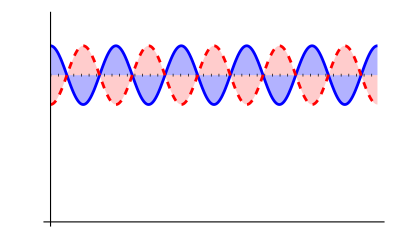

```mathematica
Plot[{1,1+0.1Cos[π x],1-0.1 Cos[π x]},{x,0,10},PlotRange->{0.5,1.2},PlotStyle->{{Black,Dotted,Thickness[0.005]},{Blue,Thickness[0.005]},{Red,Dashed,Thickness[0.005]}},AxesLabel->None,Ticks->None,Filling->{2->{{1},Opacity[0.3,Blue]},3->{{1},Opacity[0.2,Red]}},AxesStyle->Thickness[0.005]]
```

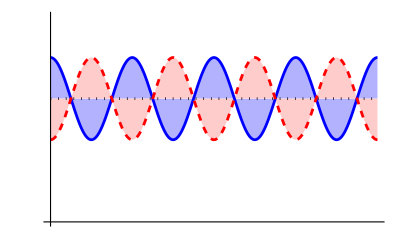

```mathematica
Plot[{1,1+0.1Cos[π x],1-0.1 Cos[π x]},{x,0,8},PlotRange->{0.7,1.2},PlotStyle->{{Black,Dotted,Thickness[0.005]},{Blue,Thickness[0.005]},{Red,Dashed,Thickness[0.005]}},AxesLabel->None,Ticks->None,Filling->{2->{{1},RGBColor[178/255,178/255,1]},3->{{1},RGBColor[1,204/255,204/255]}},AxesStyle->Thickness[0.005]]
```

```mathematica
Export["~/Desktop/test.pdf",Out[6]]
```

~/Desktop/test.pdf